```mathematica
dataStr="0,23
3,54
1,10
3,78
2,00
3,82
2,90
3,95
3,89
4,09
5,09
4,35
6,08
4,82
7,00
4,92
8,14
5,16";
```

```mathematica
data=Partition[ToExpression/@StringSplit[StringReplace[dataStr,","->"."],"\n"],2]
```

{{0.23,3.54},{1.1,3.78},{2.,3.82},{2.9,3.95},{3.89,4.09},{5.09,4.35},{6.08,4.82},{7.,4.92},{8.14,5.16}}

```mathematica
xvals=data[[All,1]];
yvals=data[[All,2]];
```

```mathematica
sx2=Total[xvals^2];
sx=Total[xvals];
sy=Total[yvals];
sprod=Total[#[[1]]#[[2]]&/@data];
n=Length[data];
{sx,sy,sx2,sprod}
```

{36.43,38.43,206.939,167.867}

```mathematica
Δ=n sx2-(sx)^2
```

535.307

```mathematica
a=1/Δ(sx2 sy-sx sprod)
b=1/Δ(n sprod-sx sy)
```

3.4322

0.206977

```mathematica
errors=(a+b #[[1]]-#[[2]])^2&/@data
```

{0.00362315,0.0144294,0.000684181,0.00679574,0.0217101,0.0184189,0.0167383,0.00151769,0.00184931}

```mathematica
Print/@errors;
```

0.00362315

0.0144294

0.000684181

0.00679574

0.0217101

0.0184189

0.0167383

0.00151769

0.00184931

```mathematica
Total[errors]
```

0.0857668

```mathematica
errsq=Total[errors]/(n-2)
```

0.0122524

```mathematica
σa=errsq/Δ sx2
σb=n errsq/Δ
```

0.00473654

0.000205997

```mathematica
LinearModelFit[data,x,x]
```

FittedModel[3.4322+0.206977 x]

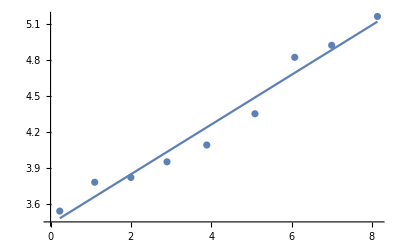

```mathematica
Show[ListPlot[data],Plot[a + b x,{x,Min[xvals],Max[xvals]}]]
```

```mathematica
yboxes[x_]:=(x-3.3)*280/(2)
```

```mathematica
Print/@({#,yboxes[#]}&/@yvals)
```

{3.54,33.6}

{3.78,67.2}

{3.82,72.8}

{3.95,91.}

{4.09,110.6}

{4.35,147.}

{4.82,212.8}

{4.92,226.8}

{5.16,260.4}

{Null,Null,Null,Null,Null,Null,Null,Null,Null}

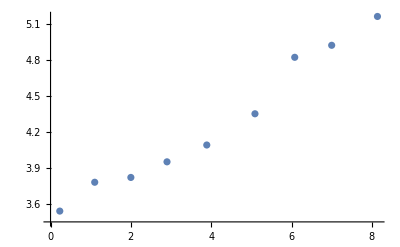

```mathematica
ListPlot[data]
```